https://cmake.org/cmake/help/v3.22/module/CMakeGraphVizOptions.html

Put  a “CMakeGraphVizOptions.cmake” in the build dir with options see link abobe...

set(GRAPHVIZ_EXECUTABLES FALSE)
set(GRAPHVIZ_MODULE_LIBS FALSE)

run cmake with --graphviz=cmake.dot

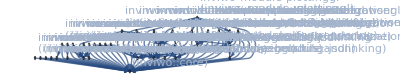

```mathematica
g = Import["/Users/peter/Documents/Inviwo/build/iwyu/cmake.dot.inviwo-core.dependers", "DOT"]
```

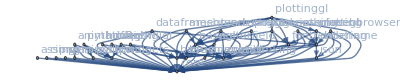

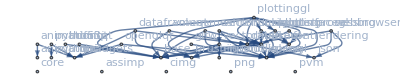

core | 31 | 0
base | 8 | 1
basegl | 5 | 4
meshrenderinggl | 0 | 4
plottinggl | 0 | 9
userinterfacegl | 1 | 4
postprocessing | 0 | 3
vectorfieldgl | 0 | 4
dataframe | 5 | 3
dataframeqt | 0 | 4
plotting | 1 | 3
volume | 0 | 3
webbrowser | 0 | 4
hdf5 | 0 | 2
nifti | 0 | 2
vectorfield | 1 | 4
animation | 1 | 1
animationqt | 0 | 3
qtwidgets | 4 | 1
openglqt | 0 | 3
python3qt | 0 | 3
assimp | 0 | 1
brushingandlinking | 4 | 1
opengl | 10 | 1
fontrendering | 3 | 2
glfw | 0 | 2
cimg | 0 | 1
json | 2 | 1
eigenutils | 1 | 1
python3 | 1 | 1
png | 0 | 1
pvm | 0 | 1

```mathematica
labels = VertexLabels/.Options[g]/.(Rule[n_,x_] :> Rule[n,StringSplit[StringSplit[x][[1]],"-"][[-1]]]);
renames={"vectorfieldvisualizationgl"->"vectorfieldgl","vectorfieldvisualization"->"vectorfield"};
vert=VertexList[g]/.labels /.renames;
edge=EdgeList[g]/.labels /.renames;



filtered ={"devtools","netcdf","pythontools", "qtapplicationbase", "qteditor"};
vert= Select[vert,(Not@MemberQ [filtered,#])&];
edge= Select[edge,(Not@MemberQ [filtered,#[[1]]] && Not@MemberQ [filtered,#[[2]]])&];

deps=Graph[vert,edge, VertexLabels->Automatic]
sub=Graph[vert, Select[edge, (#[[2]]≠"core")&], VertexLabels->Automatic]
{#,VertexInDegree[deps,#],VertexOutDegree[deps,#]}&/@VertexList[deps]//TableForm
```

```mathematica
levels[graph_]:=Module[{g=graph,result={},count = Length[VertexList[graph]],sinks},
While[Length[VertexList[g]]>0 && count >0,
count--;
sinks = Select[{#,VertexOutDegree[g,#]}&/@VertexList[g],#[[2]]==0&][[All,1]];
AppendTo[result,Sort[sinks]];
g = Graph[Select[VertexList[g],(Not@MemberQ [sinks,#])&],
Select[EdgeList[g], (Not@MemberQ[sinks,#[[2]]])&]]
];
result
];
l = levels[deps];
l//TableForm
height=Flatten@MapIndexed[#1->First@#2&,l,{2}];
edgeOneLevel=Select[edge,(( #[[1]]/.height)-(#[[2]]/.height)==1)&];
```

core |  |  |  |  |  |  |  |  |  |  | 
animation | assimp | base | brushingandlinking | cimg | eigenutils | json | opengl | png | pvm | python3 | qtwidgets
animationqt | basegl | dataframe | fontrendering | glfw | hdf5 | nifti | openglqt | python3qt | vectorfield |  | 
dataframeqt | meshrenderinggl | plotting | postprocessing | userinterfacegl | vectorfieldgl | volume | webbrowser |  |  |  | 
plottinggl |  |  |  |  |  |  |  |  |  |  |

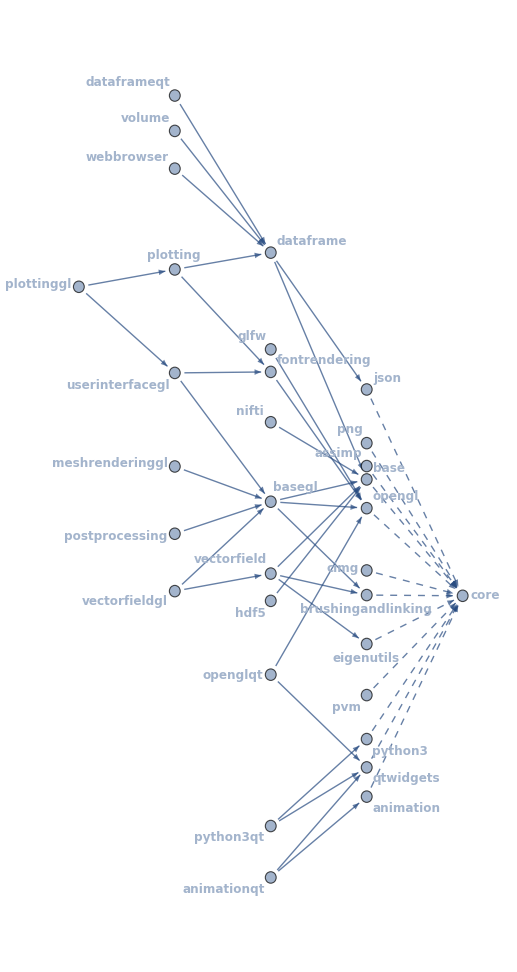

```mathematica
ef2[el_,___]:={Arrowheads[0.02],Arrow[el,0.1]}
Graph[vert, edgeOneLevel, GraphLayout->"PlanarEmbedding",
VertexCoordinates->Flatten@MapIndexed[#1->{-#2[[1]],Automatic}&,l,{2}],
EdgeStyle->Join[
((#->Dashed)&/@Select[edgeOneLevel, (#[[2]]=="core")&]),
((#->Thick)&/@Select[edgeOneLevel, (#[[2]]!="core")&])
],
EdgeShapeFunction->ef2,
VertexLabels->Automatic,
VertexLabelStyle->Directive[Bold,12]
]
```

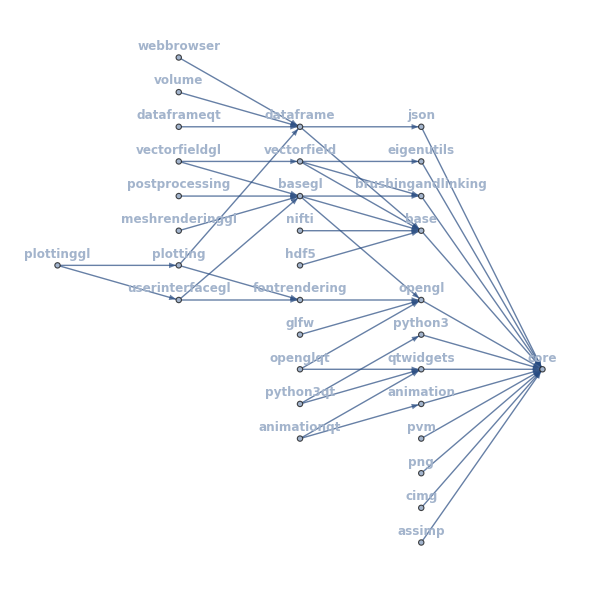

```mathematica
test=Graph[vert, edgeOneLevel, VertexLabels->Automatic,
VertexLabelStyle->Directive[Bold,12], GraphLayout->{"LayeredDigraphEmbedding", "Rotation"->90Degree}];
vertcoords=AnnotationValue[{test,#}, VertexCoordinates]&/@VertexList[test];
final=Graph[vert, edgeOneLevel, VertexLabels->Placed[Automatic,Above],
VertexCoordinates->vertcoords.{{3.5,0},{0,1}},
VertexLabelStyle->Directive[Bold,12],ImageSize->600]
```